## Single-Particle Potential Strength

```mathematica
ClearAll["Global`*"]
```

```mathematica
Vdata={2.933,3.1,1.673,8.167};
A={161,163,165,167};
tsd4={163,0.7};
```

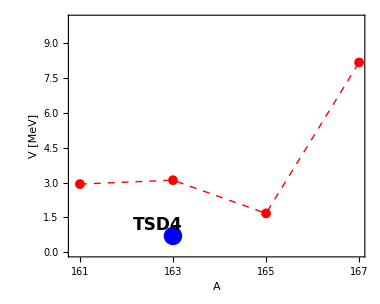

```mathematica
p1=ListPlot[Table[{A[[i]],Vdata[[i]]},{i,1,Length[A]}],AspectRatio->0.8,ImageSize->380,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Dashed,Thick},Joined->True,PlotMarkers->{Automatic, Medium},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},FrameTicks->{{Automatic,None},{{161,163,165,167},None}},PlotRange->{0,10},FrameLabel->{"A","V [MeV]"}];
Show[p1,Graphics[{Blue,PointSize[0.035],Point[{tsd4}]}],Graphics[Inset[Style["TSD4",Bold,17,FontFamily->"Arial"],Scaled[{0.3,0.13}]]]]
```